```mathematica
(* switch off message that solar panels cannot be lower than 0 degrees *)
Off[FindMinimum::reged];
Off[FindMaximum::reged];

(* Adjusting the solar panels x times a day
The times are evenly spread over the time the sun is up *)
year = 2016;

(* parameters are forced numeric, so findMaximum in dayangle works better *)
angle[i_?NumericQ,a_?NumericQ,d_]:= ( (* params: index of sunPositions table, solar panel angle in degrees, date, returns misalignment with the sun in radians *)
sunPos = sunPositions[[i]]; (* lookup sun position *)

(* remove degree unit, then convert to radians *)
gammaS= QuantityMagnitude[Quantity[sunPos[[1]]]]*Pi/180;  (* Azimuth of sun position, 0 due South, negative to the east *)
(* Because Mathematica gives azimuth in compass angle, we subtract 180 degrees *)
gammaS = gammaS - Pi;
thetaS= QuantityMagnitude[Quantity[sunPos[[2]]]]*Pi/180; (* Sun altitude *)
gammaP = 0 * Pi/180; (* Solar panels azimuth *)
thetaP = a * Pi/180; (* Solar panels angle with horizontal *)
ArcCos[Cos[gammaP-gammaS] Cos[thetaS] Sin[thetaP]+Cos[thetaP] Sin[thetaS]]
)

directPower[x_?NumericQ,a_?NumericQ,d_]  := ( (* param: index, solar panel angle in degrees, date. returns W/m^2 *)
theta=angle[x,a,d]; (* solar zenith (misalignment) in radians *)
(* here comes the magik formula from http://www.powerfromthesun.net/Book/chapter02/chapter02.html#ZEqnNum929295 for a clear day *)
n= QuantityMagnitude[Quantity[d - DateObject[{2016,1,1}]]]; (* day of year *)
i= 1367 (1+0.034 Cos[360*n/365.25]);
aZero = 0.4237 - 0.00821 36;
aOne = 0.5055 + 0.00595 6.5^2;
k = 0.2711 + 0.01858 2.5^2;
If[Cos[theta]<0,
0,
i (aZero + aOne E^(-k/Cos[theta])) (* If the sun is more than 90 degrees off, the formula is not correct, and we set the value to be 0 *)
] 
)

sumOverInterval:=Function[ (* params: solar panel angle in degrees, date, start index, end index
returns sum of solar power over the day at every hour in the given interval *)
(* take sum of every index, hence steps of one *)
Sum[directPower[i,#1,#2],{i,#3,#4,1}]
]

angleInterval := Function[ (* params: date, start index, end index, returns optimal angle in this interval *)
(* Find for which angle of the solar panels this value is maximal,starting at 0 *)
res = FindMaximum[sumOverInterval[x,#1,#2,#3],{x,0,0,90}, AccuracyGoal->5];
{res[[1]],x /. res[[2]]}
]

dayAngles := Function[ (* params: date, number of adjustment times per day ≥ 1. returns List with optimal angles and power received with that angle over that interval, for how many adjustment times were specified *)
position = GeoPosition[{51.546545,4.411744}];
sunrise = Sunrise[position,#1];
TimeZoneConvert[sunrise,2];
sunriseHour = DateValue[sunrise,"Hour"]+DateValue[sunrise, "Minute"]/60;
sunset = Sunset[position,#1];
TimeZoneConvert[sunset,2];
sunsetHour = DateValue[sunset,"Hour"] + DateValue[sunset, "Minute"]/60;

(* generate sun position table, so angle[] can access it every time *)
sunPositions = Table[
 SunPosition[GeoPosition[{51.546545,4.411744}],DateObject[#1,{h/100}]],
{h,sunriseHour*100,sunsetHour*100,10} (* steps of .1 hours, .02 doesn't help *)
];

l = Length[sunPositions];
Table[ (* calculates indices of start and end of the interval *)
angleInterval[#1,1+Round[l*i/#2],Round[l*(i+1)/#2]]
,{i,0,#2-1}]
]

dayPower[t_] := ( (* total of power *)
sum = 0;
For[i=1,i<Length[t]+1,i++,
sum += t[[i]][[1]];
];
sum (* Total of W/m^1 received *)
)

dayPowerTable[t_] := ( (* list of power received for each angle-period *)
Table[
t[[i]][[1]],
{i,1,Length[t]}
]
)

dayAnglesTable[t_] := (
(* make list of angles *)
Table[
t[[i]][[2]],
{i,1,Length[t]}
]
)

dayAngles[DateObject[{2016,7,18}],1]; (* make sure to initialize sunPositions table *)

(******************************* END OF FUNCTIONS ***************************)
(* percentages *)
(*t = Table[
dayPower[dayAngles[DateObject[{2016,7,18}],x]],
{x,1,10}
]
(* relative to first *)
Table[
(t[[i]]-t[[1]])/t[[1]],
{i,2,Length[t]}
]
(* relative to previous *)
Table[
(t[[i]]-t[[i-1]])/t[[i-1]],
{i,2,Length[t]}
]*)


(*DiscretePlot[directPower[x,30,DateObject[{2016,7,18}]],{x,81,101}]
sumOverInterval[30,DateObject[{2016,7,18}],81,91]
sumOverInterval[30,DateObject[{2016,7,18}],92,101]*)

(*DiscretePlot[sumOverInterval[x,DateObject[{2016,7,18}],81,91],{x,0,90}]
DiscretePlot[sumOverInterval[x,DateObject[{2016,7,18}],92,101],{x,0,90}]
 FindMaximum[sumOverInterval[x,DateObject[{2016,7,18}],81,91],{x,0,0,90}, AccuracyGoal->5]
FindMaximum[sumOverInterval[x,DateObject[{2016,7,18}],92,101],{x,0,0,90}, AccuracyGoal->5]*)

(* 9 (high) - 10 of 16 times -> 91-101 and 101-111*)
(* List of W/m^2 and optimal angles for this day *) 
(* table = dayAngles[DateObject[{2016,7,18}],14] ;
a= ListPlot[dayPowerTable[table]]
 table = dayAngles[DateObject[{2016,7,18}],15] ;
b=ListPlot[dayPowerTable[table]] 
 table = dayAngles[DateObject[{2016,7,18}],16] 
c = ListPlot[dayPowerTable[table]] 
 table = dayAngles[DateObject[{2016,7,18}],17] ;
d=ListPlot[dayPowerTable[table]]
 table = dayAngles[DateObject[{2016,7,18}],18] ;
e =ListPlot[dayPowerTable[table]]
Show[a,b,c,d]
Show[d,e]
 table = dayAngles[DateObject[{2016,7,18}],30] ;
f=ListPlot[dayPowerTable[table]]
 table = dayAngles[DateObject[{2016,7,18}],31] ;
g=ListPlot[dayPowerTable[table]]
Show[f,g]*)

(*DiscretePlot[ dayPower[dayAngles[DateObject[{2016,7,18}],x]],{x,1,20,1}] //Timing*)
```

{{97518.8,0.}}

{97518.8,97518.8,99614.4,100146.,100074.,99960.8,100036.,100202.,100237.,100220.}

{-1.49222×10^-16,0.0214891,0.0269413,0.0262005,0.0250416,0.025811,0.0275178,0.0278751,0.0277023}

{-1.49222×10^-16,0.0214891,0.00533747,-0.000721313,-0.00112938,0.000750613,0.00166387,0.000347719,-0.000168099}

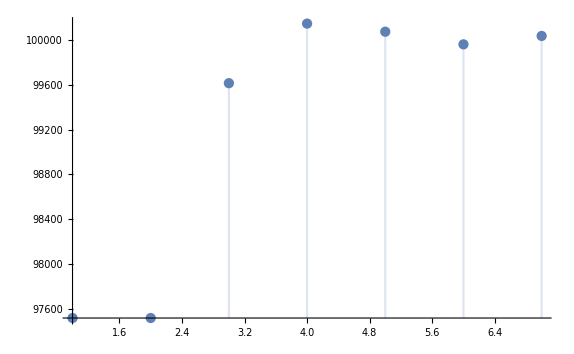
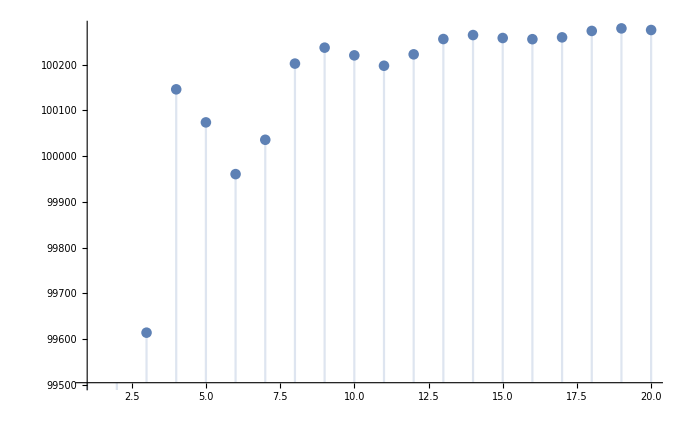
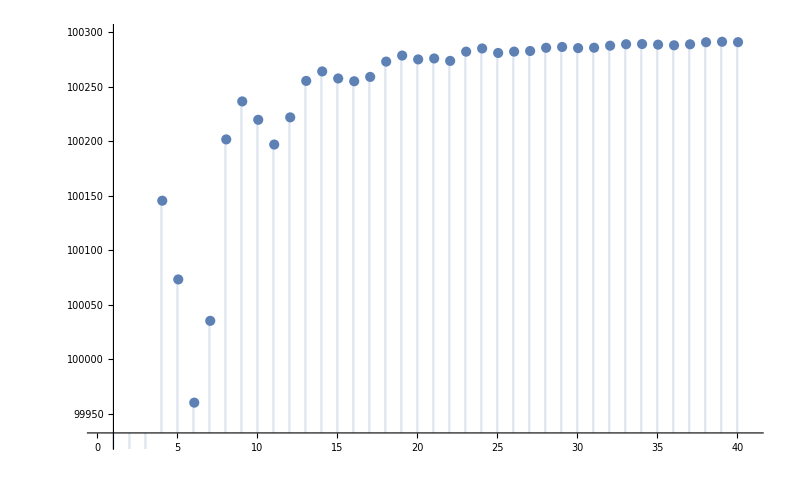
```mathematica
(* percentages change, first relative to the first, then to the previous *)
{0,0.0214891,0.0269413,0.0262005,0.0250416,0.025811,0.0275178,0.0278751,0.0277023}
{0,0.0214891,0.00533747,-0.000721313,-0.00112938,0.000750613,0.00166387,0.000347719,-0.000168099}
-Graphics--Graphics--Graphics-
```

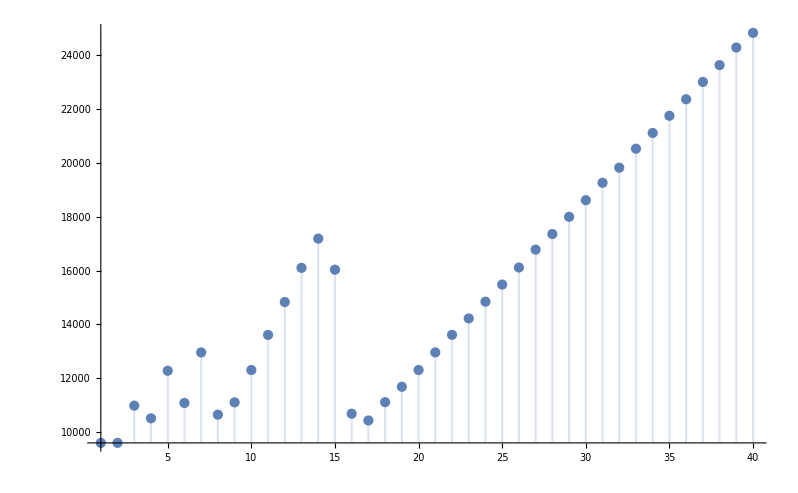
```mathematica
old -Graphics-
```